# Coupled Square Well Bound States

## Setup

Solutions of just the diagonal operator are:

```mathematica
f[L_,k_,r_]=√(π/2 k r)BesselJ[L+1/2,k r];
```

```mathematica
df[L_,k_,r_]=Simplify[D[√(π/2 k r)BesselJ[L+1/2,k r],r]];
```

```mathematica
g[L_,k_,r_]=√(π/2 k r)BesselY[L+1/2,k r];
```

```mathematica
dg[L_,k_,r_]=Simplify[D[√(π/2 k r)BesselY[L+1/2,k r],r]];
```

I’ll multiply the decaying function by a constant to rescale it for the strongly closed channels.

```mathematica
gb[L_,κ_,r_]=√(2/π κ r)BesselK[L+1/2,κ r] ⅇ^(κ Rshift)/.Rshift->0;
```

```mathematica
dgb[L_,κ_,r_]=Simplify[D[gb[L,κ,r],r]];
```

```mathematica
fb[L_,κ_,r_]=√(2/π κ r)BesselI[L+1/2,κ r];
```

```mathematica
dfb[L_,κ_,r_]=Simplify[D[√(2/π κ r)BesselI[L+1/2,κ r],r]];
```

```mathematica
SetupPotentialTriDiag[NumChan_,D0_,ϵ1_,γ_]:=
Module[{i,j,ϵthresh,Λvals,U,V},
(*ϵthresh=Table[ϵ1 (i-1),{i,1,NumChan}];*)
ϵthresh=Table[If[i==NumChan,0,i ϵ1],{i,1,NumChan}];
V=Table[If[i==j,-D0+i ϵ1-i ϵ1(KroneckerDelta[i,NumChan]),(KroneckerDelta[i,j-1]+ KroneckerDelta[i,j+1])γ],{i,1,NumChan},{j,1,NumChan}];
Λvals=Simplify[Eigenvalues[V]];
U=Transpose[Table[FullSimplify[Normalize[Eigenvectors[V][[n]]]],{n,1,NumChan}]];
{Λvals,U,ϵthresh,V}
]
```

```mathematica
TEQ0[r0_,v0_,ϵ_]:=√(v0+ϵ) Cos[r0 √(v0+ϵ)]+√-ϵ Sin[r0 √(v0+ϵ)]
```

When the energy is zero,

```mathematica
TEQ0[1,v0,0]
```

√v0 Cos[√v0]

suggests √v_0=1/2 π, 3/2 π,...

so v_0=(n+1/2)^2 π^2 with n=0,1,2,...

Solving this for n gives the approximate number of bound states as a function of the depth v_0:

n=(√v_0)/π-1/2

The number of bound states is n+1:

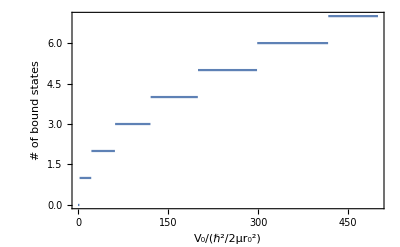

```mathematica
Plot[Floor[(√v0)/π+1/2],{v0,0,500},Frame->True,FrameLabel->{"V_0/(ℏ^2/2μr_0^2)","# of bound states"},LabelStyle->Large]
```

This is quite useful because we can immediately estimate the total density of states for an N-channel problem by noting that the total number of bound states in the uncoupled limit is:

n_tot=∑_i ((V_(i i)+ϵ_i^th)/π+1/2)

ρ=1/(∑_i ((V_(i i)+ϵ_i^th)/π+1/2))

where V_(i i)+ϵ_i^th=D_i is the total depth of the ith channel.

The energies may be easily plotted as a contour plot.  And compared to the approximate energies from the infinite square well:

√((2μ)/ℏ^2(E+V_0)) r_0=n π

ϵ =n^2 π^2-v_0

```mathematica
Table[√(ϵ+v0)==n π,{n,1,4}]
```

{√(v0+ϵ)==π,√(v0+ϵ)==2 π,√(v0+ϵ)==3 π,√(v0+ϵ)==4 π}

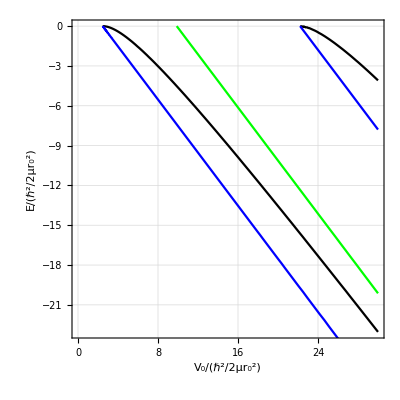

```mathematica
vmax=30;pwkb=ContourPlot[{√(ϵ+v0)==(0+1/2)π,,√(ϵ+v0)==(1+1/2)π,√(ϵ+v0)==(2+1/2)π,√(ϵ+v0)==(3+1/2)π},{v0,0,vmax},{ϵ,-v0+2,0},LabelStyle->Large,FrameLabel->{"V_0/(ℏ^2/2μr_0^2)","E/(ℏ^2/2μr_0^2)"},ContourStyle->{Blue}];
pinfwell=ContourPlot[{√(v0+ϵ)==π,√(v0+ϵ)==2 π,√(v0+ϵ)==3 π,√(v0+ϵ)==4 π},{v0,0,vmax},{ϵ,-v0+2,0},LabelStyle->Large,FrameLabel->{"V_0/(ℏ^2/2μr_0^2)","E/(ℏ^2/2μr_0^2)"},GridLines->Automatic,ContourStyle->{Green}];
pexact=ContourPlot[{TEQ0[1,v0,ϵ]==0},{v0,0,vmax},{ϵ,-v0+2,0},LabelStyle->Large,FrameLabel->{"V_0/(ℏ^2/2μr_0^2)","E/(ℏ^2/2μr_0^2)"},GridLines->Automatic,ContourStyle->{Black}];
Show[pexact,pinfwell,pwkb]
```

```mathematica
FindRoot[TEQ0[1,20,ϵ],{ϵ,-13}]
```

{ϵ→-13.5581}

Find the exact bindings using the WKB values as an initial guess:

```mathematica
r0=1;v0=400;Binding=Table[Table[If[Floor[(√v0)/π+1/2]≥n,{v0,ϵ/.FindRoot[TEQ0[r0,v0,ϵ],{ϵ,-v0+(n-1/3)^2 π^2},AccuracyGoal->5][[1]]},{,}],{v0,0,100,.1}],{n,1,Floor[(√v0)/π+1/2]}];
```

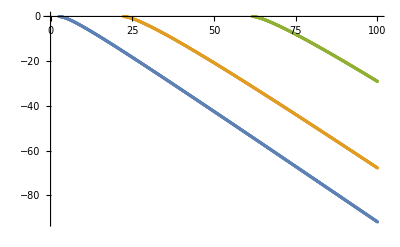

```mathematica
ListPlot[Binding]
```

```mathematica
SetupThresh[NumChan_,D0_,gscale_]:=
Module[{r0,i,j,ϵthresh,Λvals,U,V,offsets,B1,ϵ,OffsetRange,ϵ1},
r0=1;
B1 = Abs[ϵ]/.FindRoot[TEQ0[r0,D0,ϵ],{ϵ,-D0+(1-1/2)^2 π^2},AccuracyGoal->5][[1]];
Print["B1 = ",B1];
ϵ1=B1+B1/10.0;
OffsetRange=D0-ϵ1;
Print["OffsetRange = ",OffsetRange];
ϵthresh=Table[0,{i,1,NumChan}];
ϵthresh[[1;;NumChan-1]]=Sort[ϵ1+RandomReal[{0,OffsetRange},NumChan-1]];
(*ϵthresh=Table[ϵ1 (i-1),{i,1,NumChan}];*)
(*ϵthresh=Table[If[i==NumChan,0,i ϵ1],{i,1,NumChan}];*)
ϵthresh
]
```

```mathematica
ϕ[L_,λsqr_,Energy_,r_]:=If[Energy-λsqr>0,f[L,√(Energy-λsqr),r],fb[L,√(λsqr-Energy),r]];
dϕ[L_,λsqr_,Energy_,r_]:=If[Energy-λsqr>0,df[L,√(Energy-λsqr),r],dfb[L,√(λsqr-Energy),r]];
```

```mathematica
MakeΦMat[NumChan_,L_,Λ_,U_,Energy_,r_]:=Module[
{Φ,dΦ,i,j},
Φ=Table[U[[i,j]]ϕ[L,Λ[[j]],Energy,r],{i,1,NumChan},{j,1,NumChan}];
dΦ=Table[U[[i,j]]dϕ[L,Λ[[j]],Energy,r],{i,1,NumChan},{j,1,NumChan}];
{Φ,dΦ}
]
```

```mathematica
BSTEQ[Energy_,Λ_,U_,L_,ϵth_,rmatch_,NumClosed_]:=Module[{i,j,Gmat,Φ,dΦ},
Gmat=Table[0,{i,1,NumClosed},{j,1,NumClosed}];
Do[Gmat[[i,i]]=dgb[L,√(ϵth[[i]]-Energy),rmatch]/gb[L,√(ϵth[[i]]-Energy),rmatch],{i,1,NumClosed}];
{Φ,dΦ}=MakeΦMat[NumClosed,L,Λ,U,Energy,rmatch];
(*Φ=Φ[[1;;NumClosed,1;;NumClosed]];
dΦ=dΦ[[1;;NumClosed,1;;NumClosed]];*)
Det[dΦ-Gmat.Φ]
]
```

```mathematica
D0=10;
γ=0.1;
NumChan=10;
L=0;
r0=1;
ϵthresh=SetupThresh[NumChan,D0,γ];
Vdiag=Table[0,{i,1,NumChan},{j,1,NumChan}];
Do[Vdiag[[i,i]]=-D0+ϵthresh[[i]],{i,1,NumChan}];
Voffdiag=Table[(KroneckerDelta[i,j-1]+ KroneckerDelta[i,j+1])γ,{i,1,NumChan},{j,1,NumChan}];
V=Vdiag+0.1Voffdiag;
Λ=Simplify[Eigenvalues[V]];
U=Transpose[Table[FullSimplify[Normalize[Eigenvectors[V][[n]]]],{n,1,NumChan}]];
MatrixForm[V]
MatrixForm[ϵthresh]
```

B1 = 4.62419

OffsetRange = 4.91339

(-4.76501 | 0.01 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.01 | -4.5499 | 0.01 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.01 | -4.19373 | 0.01 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.01 | -3.77541 | 0.01 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.01 | -3.41566 | 0.01 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.01 | -3.01918 | 0.01 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.01 | -2.28564 | 0.01 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.01 | -1.47607 | 0.01 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.01 | -0.218005 | 0.01
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.01 | -10.)

(5.23499
5.4501
5.80627
6.22459
6.58434
6.98082
7.71436
8.52393
9.78199
0)

```mathematica
Plot[BSTEQ[Energy,Λ,U,L,r0,NumChan-1],{Energy,-D0,ϵthresh[[1]]}]
```

-Graphics-

```mathematica
BS[Energy_,λ_,NumChan_,L_,ϵthresh_,Vdiag_,Voffdiag_,r0_,NumClosed_]:=Module[{V,Λ,U},
V=Vdiag[[1;;NumClosed,1;;NumClosed]]+λ Voffdiag[[1;;NumClosed,1;;NumClosed]];
Λ=Simplify[Eigenvalues[V]];
U=Transpose[Table[FullSimplify[Normalize[Eigenvectors[V][[n]]]],{n,1,NumClosed}]];
BSTEQ[Energy,Λ,U,L,ϵthresh,r0,NumClosed]
]
```

```mathematica
BS[1.5,.1,5,0,ϵthresh,Vdiag,Voffdiag,r0,NumChan-1]
```

-0.0848884

```mathematica
L=0;
r0=1;
D0=10.0;
γ=5.0;
NumChan=10;
ϵthresh=SetupThresh[NumChan,D0,γ];
Vdiag=Table[0,{i,1,NumChan},{j,1,NumChan}];
Do[Vdiag[[i,i]]=-D0+ϵthresh[[i]],{i,1,NumChan}];
Voffdiag=Table[(KroneckerDelta[i,j-1]+ KroneckerDelta[i,j+1])γ,{i,1,NumChan},{j,1,NumChan}];
```

B1 = 4.62419

OffsetRange = 4.91339

```mathematica
MatrixForm[ϵthresh]
```

(5.70204
6.44301
6.47261
7.12511
7.27021
8.24779
8.30317
9.68183
9.83678
0)

```mathematica
NumSearch=2000;
Emin=-D0+0.001;
Emax=ϵthresh[[1]]-0.01;
λ=.01;
nc=NumChan-1;
```

```mathematica
V=Vdiag[[1;;nc,1;;nc]]+λ Voffdiag[[1;;nc,1;;nc]];
Print[MatrixForm[V]];
Λ=Simplify[Eigenvalues[V]];
U=Transpose[Table[FullSimplify[Normalize[Eigenvectors[V][[n]]]],{n,1,nc}]];
BSSectorGridSearch=Table[{Energy,BSTEQ[Energy,Λ,U,L,ϵthresh,r0,nc]},{Energy,Emin,Emax,(Emax-Emin)/(NumSearch-1)}];
```

(-3.55271 | 0.05 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.05 | -3.06166 | 0.05 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.05 | -2.88342 | 0.05 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.05 | -2.75039 | 0.05 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.05 | -1.93676 | 0.05 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.05 | -1.81687 | 0.05 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.05 | -1.47016 | 0.05 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.05 | -1.32648 | 0.05
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.05 | -0.612616)

```mathematica
Λ
```

{-3.55779,-3.07043,-2.88737,-2.73567,-1.95275,-1.80508,-1.4793,-1.31356,-0.609116}

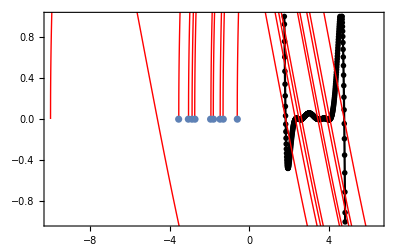

```mathematica
pl=ListPlot[BSSectorGridSearch,PlotRange->{All,{-1,1}},PlotStyle->Black,PlotMarkers->{Black,2},Joined->True, Frame->True];
puncoup=Table[Plot[TEQ0[r0,D0,ϵ]/.ϵ->Energy-ϵthresh[[i]],{Energy,-D0+ϵthresh[[i]],ϵthresh[[i]]},PlotStyle->{Red,Thin}],{i,1,NumChan}];
peigdepth=ListPlot[Table[{Λ[[i]],0},{i,1,Length[Λ]}]];
Show[pl,puncoup,peigdepth]
```

Okay, this is interesting because it tells me that the cusps in the plot of the determinant correspond to the well bottoms.  In the weak coupling limit, the zeros of the determinant coincide with the zeros of the uncoupled transcendental equations for each channel.

```mathematica
NumLam=40;dLam=1.0/(NumLam);
λ=Table[i*dLam,{i,1,NumLam}];
BSrootguess=Table[0,10];
BSroots=Table[Table[0,10],NumLam];
```

```mathematica
BSList=Table[Table[{,},{ilam,1,NumLam}],10];
```

```mathematica
Do[
V=Vdiag[[1;;nc,1;;nc]]+λ[[ilam]] Voffdiag[[1;;nc,1;;nc]];
(*Print[MatrixForm[V]];*)
Λ=Simplify[Eigenvalues[V]];
U=Transpose[Table[FullSimplify[Normalize[Eigenvectors[V][[n]]]],{n,1,nc}]];
BSSectorGridSearch=Table[{Energy,BSTEQ[Energy,Λ,U,L,ϵthresh,r0,nc]},{Energy,Emin,Emax,(Emax-Emin)/(NumSearch-1)}];
rn=1;Do[If[ Sign[BSSectorGridSearch[[i,2]]]Sign[BSSectorGridSearch[[i-1,2]]]≤ 0,BSrootguess[[rn]]=BSSectorGridSearch[[i,1]];rn+=1;],{i,2,NumSearch}];
BSrootguess=BSrootguess[[1;;rn-1]];
BSroots[[ilam]]=BSrootguess;
(*Do[BSroots[[ilam,i]]=Energy/.FindRoot[BSTEQ[Energy,Λ,U,L,ϵthresh,r0,nc]==0,{Energy,BSrootguess[[i]]}],{i,1,rn-1}];*)
Print[λ[[ilam]],BSroots[[ilam]]];
Do[BSList[[i,ilam]]={λ[[ilam]],BSroots[[ilam,i]]},{i,1,rn-1}];
,{ilam,1,NumLam}]
```

0.025{1.80816,2.28505,2.48238,2.67972,3.38683,3.60061,3.88016,4.10217,4.78461}

0.05{1.74238,2.20282,2.48238,2.7866,3.28816,3.62527,3.8555,4.18439,4.82572}

0.075{1.64371,2.10416,2.4906,2.88527,3.19772,3.60061,3.88839,4.28305,4.89972}

0.1{1.52038,2.00549,2.4906,2.93461,3.14838,3.55127,3.93772,4.38994,4.99017}

0.125{1.3806,1.90682,2.47416,2.88527,3.18127,3.51016,4.0035,4.49683,5.09706}

0.15{1.22438,1.79993,2.43305,2.81127,3.23061,3.51839,4.06928,4.60372,5.22039}

0.175{1.06815,1.68482,2.35905,2.74549,3.23061,3.56772,4.13505,4.71883,5.36017}

0.2{0.895486,1.56971,2.26038,2.68794,3.21416,3.64994,4.20905,4.83395,5.49995}

0.225{0.722819,1.4546,2.13705,2.6386,3.19772,3.74039,4.28305,4.95728,5.64795}

0.25{0.541929,1.32304,2.01371,2.58927,3.18127,3.83083,4.3735,5.08061,5.79595}

0.275{0.36104,1.19149,1.88216,2.53171,3.17305,3.91305,4.46394,5.20395,5.94395}

0.3{0.18015,1.05171,1.74238,2.47416,3.16483,3.98705,4.56261,5.32728,6.10017}

0.325{-0.00896175,0.903708,1.61082,2.40838,3.16483,4.06105,4.6695,5.45061,6.24817}

0.35{-0.198074,0.755708,1.47927,2.35083,3.16483,4.12683,4.77639,5.57395,6.4044}

0.375{-0.387185,0.599485,1.34771,2.28505,3.17305,4.18439,4.8915,5.7055}

0.4{-0.58452,0.43504,1.21615,2.21105,3.17305,4.25017,4.99839,5.82884}

0.425{-0.773631,0.278817,1.0846,2.14527,3.18127,4.30772,5.1135,5.96039}

0.45{-0.970965,0.10615,0.953042,2.07949,3.18127,4.36528,5.22039,6.08373}

0.475{-1.1683,-0.0582953,0.821486,2.00549,3.18949,4.42283,5.32728,6.20706}

0.5{-1.36563,-0.230963,0.698152,1.93971,3.18949,4.48039,5.44239,6.3304}

0.525{-1.57119,-0.40363,0.566596,1.86571,3.19772,4.53794,5.54928}

0.55{-1.76852,-0.58452,0.43504,1.79993,3.19772,4.5955,5.65617}

0.575{-1.97408,-0.757187,0.311706,1.73416,3.20594,4.65306,5.76306}

0.6{-2.17141,-0.938076,0.18015,1.66016,3.20594,4.71061,5.86173}

0.625{-2.37697,-1.11897,0.048594,1.59438,3.21416,4.76817,5.96039}

0.65{-2.58253,-1.29163,-0.082962,1.52038,3.21416,4.82572,6.05906}

0.675{-2.78808,-1.48075,-0.206296,1.4546,3.22238,4.88328,6.15773}

0.7{-2.99364,-1.66163,-0.337852,1.38882,3.22238,4.93261,6.24817}

0.725{-3.20742,-1.84252,-0.469408,1.31482,3.22238,4.99017,6.33862}

0.75{-3.41297,-2.02341,-0.600964,1.24904,3.23061,5.04772,6.42084}

0.775{-3.61853,-2.21253,-0.73252,1.18327,3.23061,5.10528}

0.8{-3.83231,-2.39342,-0.864076,1.10926,3.23061,5.15461}

0.825{-4.04609,-2.5743,-0.98741,1.04349,3.23061,5.21217}

0.85{-4.25164,-2.76342,-1.11897,0.977709,3.23883,5.26973}

0.875{-4.46542,-2.95253,-1.25052,0.903708,3.23883,5.32728}

0.9{-4.6792,-3.13342,-1.38208,0.83793,3.23883,5.37661}

0.925{-4.89298,-3.32253,-1.51363,0.76393,3.23883,5.43417}

0.95{-5.10676,-3.51164,-1.64519,0.698152,3.23883,5.4835}

0.975{-5.32054,-3.69253,-1.78497,0.632374,3.24705,5.54106}

1.{-5.53432,-3.88164,-1.91652,0.558374,3.24705,5.59039}

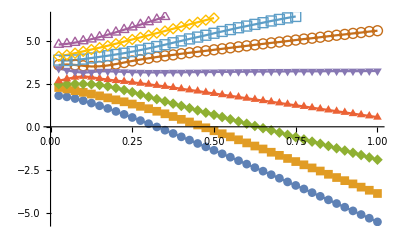

```mathematica
ListPlot[BSList,Joined->True,PlotMarkers->Automatic]
```

This looks like what I would expect!  Some avoided crossings as I crank up the couplings as well as some level repulsion.  This calculation is slow compared to Chris’s sparse matrix calculation.

```mathematica
BSroots
```

{-3.55434,1.43751,1.74004,1.89131,2.04258,2.49638,3.8578,4.00907,4.3116}

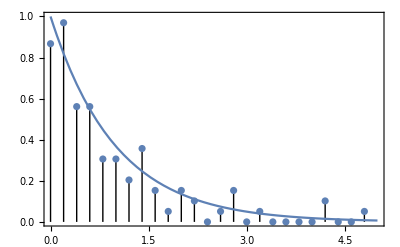

```mathematica
t1=RandomReal[{0,1},100];
lst1=Differences[Sort[t1]];
d=Mean[lst1];
dx=0.2;
ls=lst1/d;
bins=Table[t,{t,0,5,dx}];
bc1=BinCounts[ls,{bins}];
bnorm=bc1/Total[bc1]/dx;
bct2=Table[{bins[[i]],bnorm[[i]]},{i,1,Length[bins]-1}];
pt=ListPlot[bct2,Filling->Axis,FillingStyle->Black];
pp=Plot[Exp[-x],{x,0,5}];
Show[{pt,pp},Frame->True,PlotRange->All]
```

### Read in data from fortran code to generate statistical distributions

```mathematica
offsetdataspacings=Transpose[Import["~/Code/Nchannel/Square/CODES/dos/fort.99","Table"]][[1]]
```

{-19.4534,-19.1648,-18.9196,-18.7062,-18.4015,-17.9495,-17.8804,-17.7501,-17.617,-17.596,-17.5825,-17.5393,-17.4413,-17.3509,-16.5877,-16.3537,-16.1296,-15.9766,-15.8851,-15.5379,-15.4996,-15.3442,-15.2725,-15.2701,-14.8216,-14.8012,-14.5614,-14.4154,-13.6749,-13.5524,-13.1624,-13.0325,-12.3927,-12.0642,-12.0364,-12.0186,-11.8476,-11.6008,-11.5867,-11.4295,-11.1496,-11.1465,-11.1096,-11.032,-10.9065,-10.8195,-10.7769,-10.7157,-10.597}

```mathematica
pos=Differences[offsetdataspacings]
```

{0.28854,0.245191,0.213451,0.304663,0.452066,0.0690389,0.130356,0.133043,0.0210035,0.0135383,0.0431359,0.0980906,0.0903982,0.763198,0.234007,0.224023,0.153008,0.0914946,0.347212,0.0383343,0.155384,0.0717462,0.00232317,0.44857,0.0203397,0.239781,0.146072,0.740463,0.122488,0.390041,0.129885,0.63981,0.328522,0.0277812,0.0178082,0.170961,0.246843,0.014057,0.15725,0.279868,0.003095,0.036937,0.0775414,0.125478,0.0870566,0.0425865,0.0612202,0.118712}

0.184509

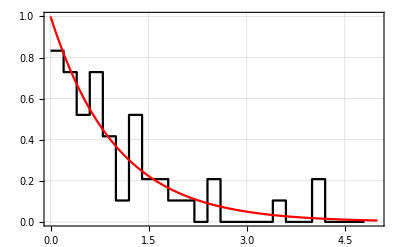

```mathematica
avgd=Mean[pos]
dx=0.2;
pos1=pos/avgd;
bins=Table[x,{x,0,5,dx}];
bc1=BinCounts[pos1,{bins}];
bcnorm=Table[{bins[[i]],bc1[[i]]/Total[bc1]/dx},{i,1,Length[bins]-1}];
Show[ListPlot[bcnorm,PlotRange->All,InterpolationOrder->0,Joined->True,PlotStyle->Black],Plot[Exp[-x],{x,0,5},PlotStyle->Red],PlotRange->All,Frame->True,GridLines->Automatic]
```

### Brody Parameter

Fit the level spacing distribution to:

```mathematica
PBrody[w_,x_]:=(1+w)(Gamma[(2+w)/(1+w)])^(1+w)x^w Exp[-(Gamma[(2+w)/(1+w)]x)^(1+w)];
αBrody[w_]:=Gamma[(2+w)/(1+w)]^(1+w);
ABrody[w_]:=αBrody[w](1+w);
```

```mathematica
CBrody[w_,z_]:=1-Exp[-αBrody[w] z^(1+w)]
```

```mathematica
D[CBrody[w,z],z]
```

ⅇ^(-z^(1+w) Gamma[(2+w)/(1+w)]^(1+w)) (1+w) z^w Gamma[(2+w)/(1+w)]^(1+w)

```mathematica
Solve[u==CBrody[w,z],z]//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{z→(-Gamma[(2+w)/(1+w)]^(-1-w) Log[1-u])^(1/(1+w))}}

```mathematica
BrodySample[w_,n_]:=Module[{u,z},u=RandomReal[{0,1},n];(-Gamma[(2+w)/(1+w)]^(-1-w) Log[1-u])^(1/(1+w))]
```

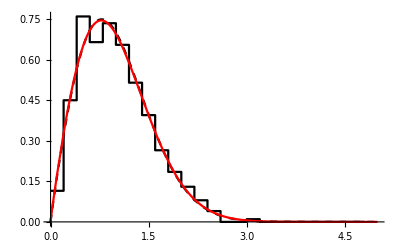

```mathematica
w0=0.954;
NP=1000;
dx=0.2;
Bins=Table[t,{t,0,5,dx}];
samp=BrodySample[w0,NP];
bc=BinCounts[samp,{Bins}]/NP/dx;
bnorm=Table[{(Bins[[i]]),bc[[i]]},{i,1,Length[Bins]-1}];
bfit=Table[{(Bins[[i]]+Bins[[i+1]])/2,bc[[i]]},{i,1,Length[Bins]-1}];
ph=ListPlot[bnorm,InterpolationOrder->0,Joined->True,PlotStyle->Black];
pe=Plot[PBrody[w0,z],{z,0,5},PlotStyle->{Black,Dashed}];
nlm=NonlinearModelFit[bfit,{PBrody[w,z]},{{w,0}},z,Method->"LevenbergMarquardt",ConfidenceLevel->0.99];
pb=Plot[PBrody[w/.nlm["BestFitParameters"],z],{z,0,5},PlotStyle->{Red}];
Show[{ph,pe,pb},PlotRange->All]
```

```mathematica
nlm["BestFitParameters"]
nlm["FitResiduals"]
```

{w→1.00859}

{-0.00829673,0.0137383,-0.0944392,0.0704419,-0.0809415,-0.0158761,0.0763439,-0.0485013,0.044066,0.00544706,0.0175743,0.0041381,-0.0133591,-0.00341626,-0.000919928,0.0075619,0.00906226,-0.000336986,0.00488681,-0.000035546,-0.0000104398,-2.8682×10^-6,-7.37259×10^-7,-1.77337×10^-7,-3.99216×10^-8}

NOTE:  The next bit of code is somewhat legacy code.  It will only work for an ensemble of one data set.  If using dos.f90, (as of 7/17) set NumEnsemble=1 in dospar.dat

```mathematica
Bdata1=Import["~/Code/Nchannel/Square/CODES/dos/fort.300","Table"];
Length[Bdata1]
```

2100

0.166797

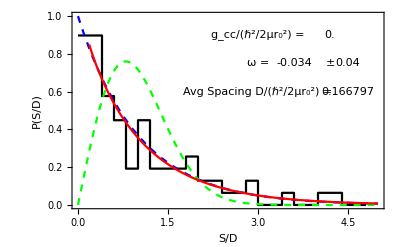

```mathematica
i=1;
l1=Length[Bdata1[[i]]];
b1=Bdata1[[i]][[2;;l1]];
d=Mean[b1]
ns=l1+1;
dos = 1/d;
b1=b1/d;
dx=0.2;
bins=Table[sd,{sd,0,5,dx}];
bc=BinCounts[b1,{bins}];
bnorm=bc/Total[bc]/dx;
bd=Table[{bins[[i]],bnorm[[i]]},{i,1,Length[bins]-1}];
bfit=Table[{(bins[[i]]+bins[[i+1]])/2,bnorm[[i]]},{i,1,Length[bins]-1}];
nlm=NonlinearModelFit[bfit,{PBrody[w,z]},{{w,0.5}},z,Method->"LevenbergMarquardt",ConfidenceLevel->0.99];
pp=Plot[{PBrody[0,x],PBrody[1,x]},{x,0,5},PlotStyle->{{Blue,Dashed},{Green,Dashed}}];
ph=ListPlot[bd,PlotStyle->Black,Joined->True,InterpolationOrder->0,PlotRange->All];
pbrody=Plot[PBrody[w/.nlm["BestFitParameters"],z],{z,0.0,5},PlotStyle->{Red}];
Show[{ph,pp,pbrody},Frame->True,PlotRange->All,Epilog->{
Text["g_cc/(ℏ^2/2μr_0^2) = ",{3,.9}],
Text[Bdata1[[i]][[1]],{4.2,0.9}],
Text["ω = ",{3,.75}],
Text[NumberForm[w/.nlm["BestFitParameters"],2],{3.6,0.75}],
Text["±",{4.2,0.75}],
Text[NumberForm[nlm["ParameterErrors"][[1]],1],{4.5,0.75}],
Text["Avg Spacing D/(ℏ^2/2μr_0^2) = ",{3.0,0.6}],
Text[d,{4.5,0.6}]
},LabelStyle->Large,FrameLabel->{"S/D","P(S/D)"}]
```

```mathematica
brodyparams=Table[l1=Length[Bdata1[[i]]];
b1=Bdata1[[i]][[2;;l1]];
d=Mean[b1];
ns=l1+1;
dos = 1/d;
b1=b1/d;
dx=0.2;
bins=Table[sd,{sd,0,5,dx}];
bc=BinCounts[b1,{bins}];
bnorm=bc/Total[bc]/dx;
bfit=Table[{(bins[[i]]+bins[[i+1]])/2,bnorm[[i]]},{i,1,Length[bins]-1}];
nlm=NonlinearModelFit[bfit,{PBrody[w,z]},{{w,0.5}},z,Method->"LevenbergMarquardt",ConfidenceLevel->0.99];
{{Bdata1[[i]][[1]]/d,w/.nlm["BestFitParameters"]},ErrorBar[nlm["ParameterErrors"][[1]]]}
,{i,1,Length[Bdata1]}]
```

{{{0.,-0.0344313},ErrorBar[0.0446191]},{{0.332723,0.392478},ErrorBar[0.185794]},{{0.663387,0.733435},ErrorBar[0.185875]},{{0.990141,0.908711},ErrorBar[0.191739]},{{1.3114,0.975254},ErrorBar[0.295477]},{{1.62631,1.1504},ErrorBar[0.294103]},{{1.93422,1.43062},ErrorBar[0.447864]},{{2.23497,1.56381},ErrorBar[0.467313]},{{2.52846,1.7732},ErrorBar[0.435802]},{{2.81484,2.42478},ErrorBar[0.386119]}}

```mathematica
Needs["ErrorBarPlots`"]
```

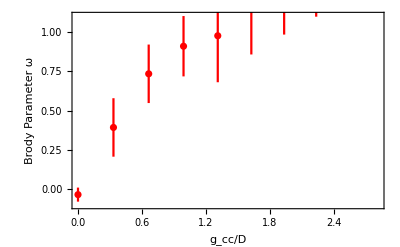

```mathematica
pnew=ErrorListPlot[brodyparams,PlotRange->{All,{-0.1,1.1}},Frame->True,LabelStyle->Large,FrameLabel->{"g_cc/D","Brody Parameter ω"},PlotStyle->Red]
```

```mathematica
pold=ErrorListPlot[brodyparams,PlotRange->{All,{-0.1,1.1}},Frame->True,LabelStyle->Large,FrameLabel->{"g_cc/D","Brody Parameter ω"}]
```

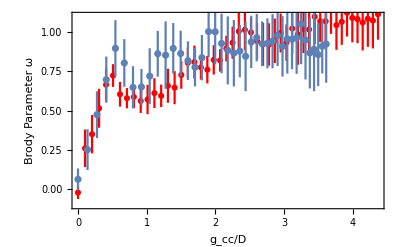

```mathematica
Show[{pnew,pold}]
```

```mathematica
bc/Total[bc]
```

{19/98,12/49,1/7,1/14,2/49,5/98,3/49,3/98,5/98,1/98,3/98,1/49,1/49,0,0,0,1/49,1/98,0,0}

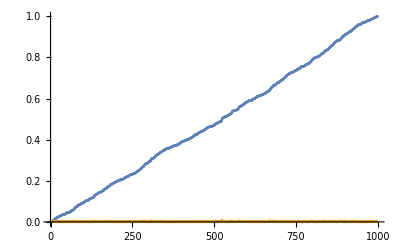

{a→3.09088×10^-9}

{0.,0.00010103}

```mathematica
t1=RandomReal[{0,1},1000];
lst1=Differences[Sort[t1]];
d=Mean[lst1];
dx=0.2;
ls=lst1/d;
bins=Table[t,{t,0,5,dx}];
bc1=BinCounts[ls,{bins}];
bnorm=bc1/Total[bc1]/dx;
w0=0.0;
α0=αBrody[w0];
ϕtest=1-Exp[-α0 ls^(1+w0)];
ϕi=Sort[ϕtest];
di=Differences[ϕi];
ListPlot[{ϕi,di}]
FindFit[Sort[di],{a y^2},{a},y]
{w0,b/a/.FindFit[ϕi,{a y + b y^2},{a,b},y]}
```

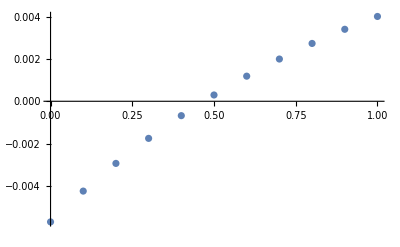

```mathematica
ListPlot[Table[
α0=αBrody[w0];
ϕtest=1-Exp[-α0 ls^(1+w0)];
ϕi=Sort[ϕtest];{w0,b/.FindFit[ϕi,{a y + b y^2},{a,b},y]},{w0,0,1,0.1}]]
```